## Leslie-Gower model

### Variables & Parameters

```mathematica
(* Population density of species 1 & 2 *)
N1=.;N2=.;
(* Trait of species 1 & 2 and the optimum trait *)
x=.;x2=.;h=.;
(* Coefficients of intraspecific competition of species 1 & 2 *)
alpha11 =.;alpha22 =.;
(* Maximum values of coefficients of interspecific competition *)
betaMax=.;
(* Maximum values of fecundity *)
lambdaMax=.;
```

### Functions for competition and fertilization

#### Competition

```mathematica
alpha12 =betaMax Exp[-(x-x2)^2];
alpha21 =betaMax Exp[-(x2-x)^2];
```

#### Fertilization

```mathematica
lambda1 =lambdaMax Exp[-(x-h)^2];
lambda2 =lambdaMax Exp[-(x2-h)^2];
```

### Base equation

```mathematica
sp1dens = (lambda1 N1)/(1+alpha11 N1 + alpha12 N2);
sp2dens = (lambda2 N2)/(1+alpha22 N2 + alpha21 N1);
fitness=D[Log[sp1dens/N1],x];
```

### Setting parameters

```mathematica
par={x2-> -0.1,h-> 0,alpha11-> 1,alpha22-> 1,betaMax-> 1.1,lambdaMax-> 100};
```

### Nullicline

#### Evolution reached the optimum trait

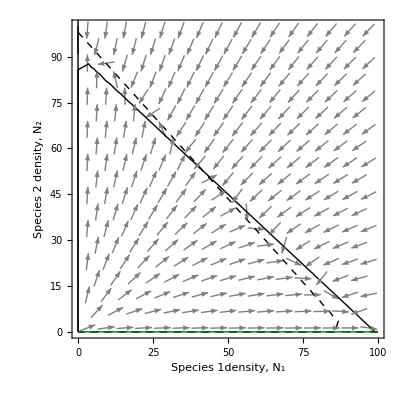

```mathematica
psp1dens=sp1dens/.par/.{x-> 0.};
psp2dens=sp2dens/.par/.{x-> 0.};
pfitness=fitness/.par/.{x-> 0.};

xMin=-0.01;xMax=100;yMin=-0.01;yMax=100;

cp1=ContourPlot[{psp1dens-N1==0},{N1,xMin,xMax},{N2,yMin,yMax},ContourStyle->{Black,Thick}];
cp2=ContourPlot[psp2dens-N2==0,{N1,xMin,xMax},{N2,yMin,yMax},ContourStyle->{Black,Dashed,Thick}];
cp3=ContourPlot[pfitness==0,{N1,xMin,xMax},{N2,yMin,yMax},ContourStyle->{RGBColor[0,0.5,0],Thick}];
vecP = VectorPlot[ {psp1dens-N1,psp2dens-N2},{N1,xMin,xMax},{N2,yMin,yMax},
VectorColorFunction->None, VectorStyle->{Gray}];
gl1=Graphics[{Thick,Black,Line[{{0,0},{0,200}}]}];
gl2=Graphics[{Thick,Dashed,Black,Line[{{0,0},{2000,0}}]}];

Show[vecP,gl1,gl2,cp1,cp2,cp3,
PlotLabel->None,LabelStyle->{FontFamily->"Helvetica Neue",18,GrayLevel[0]},FrameLabel->{{RawBoxes[RowBox[{RowBox[{"Species"," ","2"," ","density"}],","," ",StyleBox[SubscriptBox["N",StyleBox["2",FontSlant->"Plain"]],FontSlant->"Italic"]}]],None},{RawBoxes[RowBox[{RowBox[{"Species"," ","1","density"}],","," ",StyleBox[SubscriptBox["N",StyleBox["1",FontSlant->"Plain"]],FontSlant->"Italic"]}]],None}},PlotLabel->None
]
```

#### Evolution reached the trait at which coexistence is possible

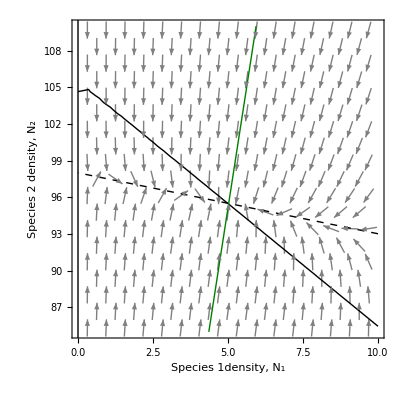

```mathematica
psp1dens=sp1dens/.par/.{x-> 0.79};
psp2dens=sp2dens/.par/.{x-> 0.79};
pfitness=fitness/.par/.{x-> 0.79};

xMin=0;xMax=10;yMin=85;yMax=110;

cp1=ContourPlot[{psp1dens-N1==0},{N1,xMin,xMax},{N2,yMin,yMax},ContourStyle->{Black,Thick}];
cp2=ContourPlot[psp2dens-N2==0,{N1,xMin,xMax},{N2,yMin,yMax},ContourStyle->{Black,Dashed,Thick}];
cp3=ContourPlot[pfitness==0,{N1,xMin,xMax},{N2,yMin,yMax},ContourStyle->{RGBColor[0,0.5,0],Thick}];
vecP = VectorPlot[ {psp1dens-N1,psp2dens-N2},{N1,xMin,xMax},{N2,yMin,yMax},
VectorColorFunction->None, VectorStyle->{Gray}];
gl1=Graphics[{Thick,Black,Line[{{0,0},{0,200}}]}];
gl2=Graphics[{Thick,Dashed,Black,Line[{{0,0},{2000,0}}]}];

Show[vecP,gl1,gl2,cp1,cp2,cp3,
PlotLabel->None,LabelStyle->{FontFamily->"Helvetica Neue",18,GrayLevel[0]},FrameLabel->{{RawBoxes[RowBox[{RowBox[{"Species"," ","2"," ","density"}],","," ",StyleBox[SubscriptBox["N",StyleBox["2",FontSlant->"Plain"]],FontSlant->"Italic"]}]],None},{RawBoxes[RowBox[{RowBox[{"Species"," ","1","density"}],","," ",StyleBox[SubscriptBox["N",StyleBox["1",FontSlant->"Plain"]],FontSlant->"Italic"]}]],None}},PlotLabel->None
]
```

## Lotka-Volterra model

### Variables & Parameters

```mathematica
N1=.;N2=.;
x=.;x2=.;h=.;
alpha11 =.;alpha22 =.;
betaMax=.;rMax=.;
```

### Functions for competition and fertilization

#### Competition

```mathematica
alpha12 =betaMax Exp[-(x-x2)^2];
alpha21 =betaMax Exp[-(x2-x)^2];
```

#### Fertilization

```mathematica
r1 =rMax Exp[-(x-h)^2];
r2 =rMax Exp[-(x2-h)^2];
```

### Base equation

```mathematica
sp1dens = N1(r1-alpha11 N1 -alpha12 N2);
sp2dens = N2(r2-alpha21 N1 -alpha22 N2);
fitness= D[sp1dens/N1,x];
```

### Setting parameters

```mathematica
par={x2-> -0.1,h-> 0,alpha11-> 1,alpha22-> 1,betaMax-> 1.1,rMax-> 100};
```

### Nullincline

#### Evolution reached the optimum trait

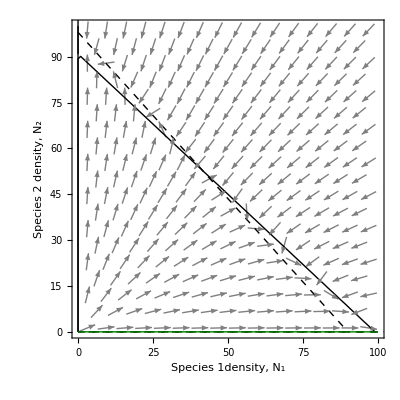

```mathematica
psp1dens=sp1dens/.par/.{x-> 0};
psp2dens=sp2dens/.par/.{x-> 0};
pfitness=fitness/.par/.{x-> 0};

xMin=-0.01;xMax=100;yMin=-0.01;yMax=100;

cp1=ContourPlot[{psp1dens-N1==0},{N1,xMin,xMax},{N2,yMin,yMax},ContourStyle->{Black,Thick}];
cp2=ContourPlot[psp2dens-N2==0,{N1,xMin,xMax},{N2,yMin,yMax},ContourStyle->{Black,Dashed,Thick}];
cp3=ContourPlot[pfitness==0,{N1,xMin,xMax},{N2,yMin,yMax},ContourStyle->{RGBColor[0,0.5,0],Thick}];
vecP = VectorPlot[ {psp1dens-N1,psp2dens-N2},{N1,xMin,xMax},{N2,yMin,yMax},
VectorColorFunction->None, VectorStyle->{Gray}];
gl1=Graphics[{Thick,Black,Line[{{0,0},{0,200}}]}];
gl2=Graphics[{Thick,Dashed,Black,Line[{{0,0},{2000,0}}]}];

Show[vecP,gl1,gl2,cp1,cp2,cp3,
PlotLabel->None,LabelStyle->{FontFamily->"Helvetica Neue",18,GrayLevel[0]},FrameLabel->{{RawBoxes[RowBox[{RowBox[{"Species"," ","2"," ","density"}],","," ",StyleBox[SubscriptBox["N",StyleBox["2",FontSlant->"Plain"]],FontSlant->"Italic"]}]],None},{RawBoxes[RowBox[{RowBox[{"Species"," ","1","density"}],","," ",StyleBox[SubscriptBox["N",StyleBox["1",FontSlant->"Plain"]],FontSlant->"Italic"]}]],None}},PlotLabel->None
]
```

#### Evolution reached the trait at which coexistence is possible

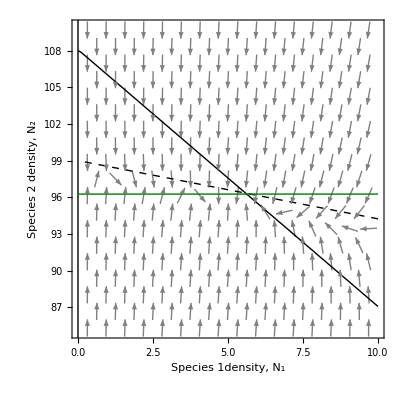

```mathematica
psp1dens=sp1dens/.par/.{x-> 0.815};
psp2dens=sp2dens/.par/.{x-> 0.815};
pfitness=fitness/.par/.{x-> 0.815};

xMin=0;xMax=10;yMin=85;yMax=110;

cp1=ContourPlot[psp1dens==0,{N1,xMin,xMax},{N2,yMin,yMax},ContourStyle->{Black,Thick}];
cp2=ContourPlot[psp2dens==0,{N1,xMin,xMax},{N2,yMin,yMax},ContourStyle->{Black,Dashed,Thick}];
cp3=ContourPlot[pfitness==0,{N1,xMin,xMax},{N2,yMin,yMax},ContourStyle->{RGBColor[0,0.5,0],Thick}];
vecP = VectorPlot[ {psp1dens-N1,psp2dens-N2},{N1,xMin,xMax},{N2,yMin,yMax},
VectorColorFunction->None, VectorStyle->{Gray}];
gl1=Graphics[{Thick,Black,Line[{{0,0},{0,200}}]}];
gl2=Graphics[{Thick,Dashed,Black,Line[{{0,0},{2000,0}}]}];

Show[vecP,gl1,gl2,cp1,cp2,cp3,
PlotLabel->None,LabelStyle->{FontFamily->"Helvetica Neue",18,GrayLevel[0]},FrameLabel->{{RawBoxes[RowBox[{RowBox[{"Species"," ","2"," ","density"}],","," ",StyleBox[SubscriptBox["N",StyleBox["2",FontSlant->"Plain"]],FontSlant->"Italic"]}]],None},{RawBoxes[RowBox[{RowBox[{"Species"," ","1","density"}],","," ",StyleBox[SubscriptBox["N",StyleBox["1",FontSlant->"Plain"]],FontSlant->"Italic"]}]],None}},PlotLabel->None
]
```